### TASK: Which distribution?

Together with this notebook there is a package file Project2.m with a random number generator from secret distributions. Put the package file in the same directory as this notebook. You load the package (once a session) with the following code:
You can then use the method randomNumber[i, n] to generate n random numbers from distribution i. For example,

```mathematica
SetDirectory[NotebookDirectory[]];
Once[Get["Project2.m","IX1501"]];
?randomNumber
randomNumber[3,10];
```

randomNumber[i, n] gives n randomnumbers from secret distribution i, i=0,1,...,6.

In this task, randomNumber[i, n] can be used to generate data for the distributions i=1,2,…,6. They are all distributions that are mentioned in the course literature (Blom Sec. 3.4 and Sec. 3.6). Do the following assignments for each of six distributions, i.e. i∈{1,2,…,6}.

Use the straight line approach to determine a distribution model.

Determine point estimates of the parameters.

Compute 95% confidence intervals for the parameters. The interval should not be longer than 10% of its mean, e.g. μ (1±0.05).

## Declaration and Introduction

```mathematica
(* declare and generate the 6 unknown distributions *)
(* sort and plot the n points of the distributions *)
n=1000;
𝕩1=randomNumber[1,n];
𝕩2=randomNumber[2,n];
𝕩3=randomNumber[3,n];
𝕩4=randomNumber[4,n];
𝕩5=randomNumber[5,n];
𝕩6=randomNumber[6,n];
𝕩1sort=Sort[𝕩1];
𝕩2sort=Sort[𝕩2];
𝕩3sort=Sort[𝕩3];
𝕩4sort=Sort[𝕩4];
𝕩5sort=Sort[𝕩5];
𝕩6sort=Sort[𝕩6];
```

```mathematica
(* facit *)
(*
FindDistribution[𝕩1];
FindDistribution[𝕩2];
FindDistribution[𝕩3];
FindDistribution[𝕩4];
FindDistribution[𝕩5];
FindDistribution[𝕩6];
𝕩1 : ExponentialDistribution[4.52875]
𝕩2 : GeometricDistribution[0.06462]
𝕩3 : GammaDistribution[7.09714,1.80106]
𝕩4 : NormalDistribution[3.00109,5.21337]
𝕩5 : BinomialDistribution[11,0.30072]
𝕩6 : PoissonDistribution[9.881]
*)
```

```mathematica
ListPlot[𝕩1sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Red,PlotLabel->"𝕩1"];
ListPlot[𝕩2sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Green,PlotLabel->"𝕩2"];
ListPlot[𝕩3sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Blue,PlotLabel->"𝕩3"];
ListPlot[𝕩4sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Yellow,PlotLabel->"𝕩4"];
ListPlot[𝕩5sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Purple,PlotLabel->"𝕩5"];
ListPlot[𝕩6sort,AxesLabel->{HoldForm[x],HoldForm[y]},PlotStyle->Gray,PlotLabel->"𝕩6"];

(* Below: Plot all the unknown functions in sorted form *)
```

```mathematica
(* 
Let each value correspond to and increase of Δ=1/n probability. Also let each value correspond to the mid point in the Δinterval so the first value Subscript[x, 1] corresponds to P(X≤Subscript[x, 1])=Δ/2 and the value Subscript[x, k] to P(X≤Subscript[x, k])=Δ/2+(k-1) Δ. 
*)
```

```mathematica
Δ=1/n;
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
(* lineplot to be used to compare the data to the model, declared "globally" here *)
lineplot=Plot[x,{x,0,1}];
```

```mathematica
𝕩1𝕡data=Transpose[{𝕩1sort,𝕡data}];
𝕩2𝕡data=Transpose[{𝕩2sort,𝕡data}];
𝕩3𝕡data=Transpose[{𝕩3sort,𝕡data}];
𝕩4𝕡data=Transpose[{𝕩4sort,𝕡data}];
𝕩5𝕡data=Transpose[{𝕩5sort,𝕡data}];
𝕩6𝕡data=Transpose[{𝕩6sort,𝕡data}];
```

```mathematica
ListPlot[𝕩1𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Red,PlotLabel->"𝕩1"];
ListPlot[𝕩2𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Green,PlotLabel->"𝕩2"];
ListPlot[𝕩3𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Blue,PlotLabel->"𝕩3"];
ListPlot[𝕩4𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Yellow,PlotLabel->"𝕩4"];
ListPlot[𝕩5𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Purple,PlotLabel->"𝕩5"];
ListPlot[𝕩6𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]},PlotStyle->Gray,PlotLabel->"𝕩6"];
```

From the plots it can be concluded that the unknown distributions 𝕩2, 𝕩5 and  𝕩6 are discrete. Distributions 𝕩1,  𝕩3 and 𝕩4 are continuous. The discrete and and continuous cases will be studied separately.

## Straight Line Approach

Discrete distributions [𝕩2, 𝕩5, 𝕩6]

### Distribution 𝕩2

```mathematica
(* 𝕩2 : Geometric distribution model-data setup *)
Clear[p];
𝒢GeoDist𝕩2=EstimatedDistribution[𝕩2,GeometricDistribution[p]]
𝕡modelGeoDist𝕩2=CDF[𝒢GeoDist𝕩2,𝕩2sort];
comparedataGeoDist𝕩2=Transpose[{𝕡modelGeoDist𝕩2,𝕡data}];
dataplotGeoDist𝕩2=ListPlot[comparedataGeoDist𝕩2,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Geometric",AspectRatio->Automatic];
```

GeometricDistribution[0.0628457]

### Distribution 𝕩5

```mathematica
(* 𝕩5 : Binomial distribution model-data setup *)
Clear[n,p];
𝒢BinDist𝕩5=EstimatedDistribution[𝕩5,BinomialDistribution[n,p]];
𝕡modelBinDist𝕩5=CDF[𝒢BinDist𝕩5,𝕩5sort];
comparedataBinDist𝕩5=Transpose[{𝕡modelBinDist𝕩5,𝕡data}];
dataplotBinDist𝕩5=ListPlot[comparedataBinDist𝕩5,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Binomial",AspectRatio->Automatic];
```

### Distribution 𝕩6

```mathematica
(* 𝕩6 : Poisson distribution model-data setup *)
Clear[μ];
𝒢PoDist𝕩6=EstimatedDistribution[𝕩6,PoissonDistribution[μ]];
𝕡modelPoDist𝕩6=CDF[𝒢PoDist𝕩6,𝕩6sort];
comparedataPoDist𝕩6=Transpose[{𝕡modelPoDist𝕩6,𝕡data}];
dataplotPoDist𝕩6=ListPlot[comparedataPoDist𝕩6,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Poisson",AspectRatio->Automatic];
```

Graph Discrete Distributions

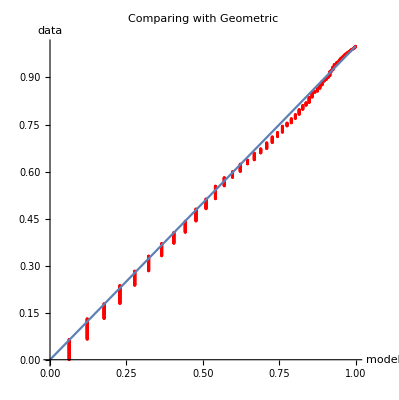

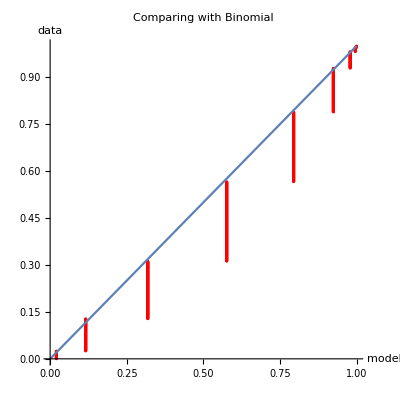

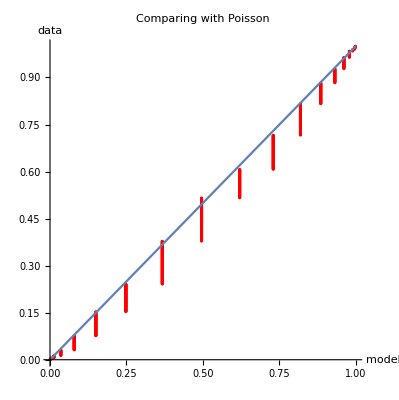

```mathematica
Show[dataplotGeoDist𝕩2, lineplot] 
Show[dataplotBinDist𝕩5, lineplot] 
Show[dataplotPoDist𝕩6, lineplot]
```

Continuous distributions [𝕩1, 𝕩3, 𝕩4]

### Distribution 𝕩1

```mathematica
(* 𝕩1 : Exponential distribution model-data setup *)
𝒢ExpDist𝕩1=EstimatedDistribution[𝕩1,ExponentialDistribution[λ]];
𝕡modelExpDist𝕩1=CDF[𝒢GammaDistr𝕩1,𝕩1sort];
comparedataExpDist𝕩1=Transpose[{𝕡modelExpDist𝕩1,𝕡data}];
dataplotExpDist𝕩1=ListPlot[comparedataExpDist𝕩1,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Exponential",AspectRatio->Automatic];
```

### Distribution 𝕩3

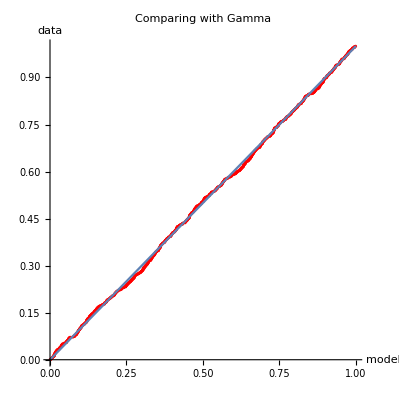

```mathematica
(* 𝕩3 : Gamma distribution model-data setup *)
Clear[α,β];
𝒢GammaDist𝕩3=EstimatedDistribution[𝕩3,GammaDistribution[α,β]];
𝕡modelGammaDist𝕩3=CDF[𝒢GammaDist𝕩3,𝕩3sort];
comparedataGammaDist𝕩3=Transpose[{𝕡modelGammaDist𝕩3,𝕡data}];
dataplotGammaDist𝕩3=ListPlot[comparedataGammaDist𝕩3,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Gamma",AspectRatio->Automatic];
```

### Distribution 𝕩4

```mathematica
(* 𝕩4 : Normal distribution model-data setup *)
x4=Mean[𝕩4];
s4=StandardDeviation[𝕩4];
𝒩4=NormalDistribution[x4,s4];
𝕡modelNormalDist𝕩4=CDF[𝒩4,𝕩4sort];
comparedataNormalDist𝕩4=Transpose[{𝕡modelNormalDist𝕩4,𝕡data}];
dataplotNormalDist𝕩4=ListPlot[comparedataNormalDistr𝕩4,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"Comparing with Normal",AspectRatio->Automatic];
```

Graph Continuous Distributions

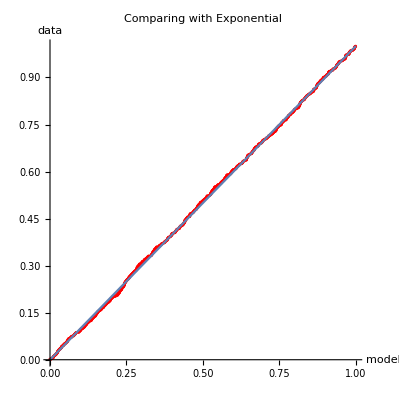

-Graphics-

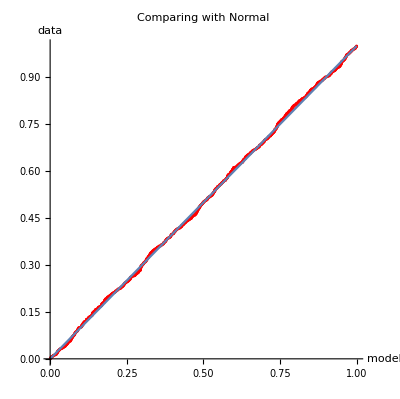

```mathematica
Show[dataplotExpDist𝕩1, lineplot] 
Show[dataplotGammaDist𝕩3,lineplot]
Show[dataplotNormalDist𝕩4,lineplot]
```

## Point Estimates of the Parameters

Parameters

Unknown Parameters:
	- μ = population mean
	- σ = population standard deviation
	- p = population proportion
Empirical Point Estimators: 
	- x^- = sample mean
	- s = sample standard deviation
	- p^- = sample proportion

## Exponential Distribution - 𝕩1

Unknown Parameters:
	- μ = population mean
	- σ = population standard deviation
	- p = population proportion
Empirical Point Estimators: 
	- x^- = sample mean
	- s = sample standard deviation
	- p^- = sample proportion

“We use our empirical data to make an estimation about some unknown population parameter”
“Tecknically, the error component in a point estimate is expressed as a confidence interval”

In point estimates, you end up with one single number which represents the number that we’re trying to estimate.

```mathematica
xBar=Total[Take[𝕩, {6, 50}]]/45
Clear[μ,σ,data];
μ=Mean[𝕩4];
σ=StandardDeviation[𝕩4];
data=RandomVariate[NormalDistribution[μ,σ],100];
Likelihood[NormalDistribution[μ,σ],data];(* Likelihood[NormalDistribution[μ,σ], { x1, x2, x3, x4, x5 }]; *)
```

0.299094

## Geometric Distribution - 𝕩2

```mathematica
Clear[μ,σ,data,p];
𝒢GeoDist𝕩2=EstimatedDistribution[𝕩2,GeometricDistribution[p]]
```

GeometricDistribution[0.0628457]

## Gamma Distribution - 𝕩3

```mathematica
Clear[μ,σ,data];
```

## Normal Distribution - 𝕩4

```mathematica
Clear[μ,σ,data];
```

## Binomial Distribution - 𝕩5

```mathematica
Clear[μ,σ,data];
```

## Poisson Distribution - 𝕩6

```mathematica
Clear[μ,σ,data];
```

## Compute 95% Confidence Intervals for the Parameters (...condition)

```mathematica
MeanCI[𝕩1, ConfidenceLevel->0.95];
```